```mathematica
ClearAll["Global`*"]
```

```mathematica
$Assumptions={(ζ1|ζ2|h|d)∈Reals(*,b>0,h>b*)};
```

ζ1 = -d/2;
ζ2 = d/2;

```mathematica
df=KK (ζ+ζ1)^(-1/2)  (ζ+ζ2)^(1/2)   (ζ)^-1  (ζ-ζ1)^(-1/2)  (ζ-ζ2)^(1/2)   // FullSimplify
```

(KK √(ζ-ζ2) √(ζ+ζ2))/(ζ √(ζ-ζ1) √(ζ+ζ1))

```mathematica
f[ζ_]=(∫dfⅆζ//FullSimplify)+F
```

F-(2 KK (ζ-ζ1)^(3/2) ζ2 √(-((ζ+ζ1) (ζ1-ζ2))/((ζ-ζ1) (ζ1+ζ2))) √(((ζ-ζ2) (ζ+ζ2) (-ζ1^2+ζ2^2))/((ζ-ζ1)^2 ζ2^2)) ((ζ1+ζ2) EllipticF[ArcSin[(√(((ζ-ζ2) (ζ1+ζ2))/((ζ-ζ1) ζ2)))/(√2)],(4 ζ1 ζ2)/(ζ1+ζ2)^2]-ζ2 EllipticPi[(2 ζ1)/(ζ1+ζ2),ArcSin[(√(((ζ-ζ2) (ζ1+ζ2))/((ζ-ζ1) ζ2)))/(√2)],(4 ζ1 ζ2)/(ζ1+ζ2)^2]-ζ1 EllipticPi[(2 ζ2)/(ζ1+ζ2),ArcSin[(√(((ζ-ζ2) (ζ1+ζ2))/((ζ-ζ1) ζ2)))/(√2)],(4 ζ1 ζ2)/(ζ1+ζ2)^2]))/(ζ1 √(ζ+ζ1) √(ζ-ζ2) √(ζ+ζ2) (ζ1+ζ2))

```mathematica
FullSimplify[f[ζ],Assumptions->{ζ1>ζ2, ζ2>0}]
```

$Aborted

```mathematica
ζ1=h;
Solve[{f[-ζ1+ϵ] == -ⅈ h,f[-ζ2+ϵ] ==-ⅈ (h-d),f[ϵ] ==inf},{KK,F,ζ2}]
```

$Aborted

```mathematica
(* Note that we have mapped (lower) step to η=-1. *)
```

```mathematica
sol=Solve[{f[ζ1]==-ⅈ h, f[ζ2]==-ⅈ (h-d)},{F,KK}]
```

{{F→(ⅈ (d Log[√-d]-h Log[√-d]+h Log[√d]))/(Log[√-d]-Log[√d]),KK→ⅈ/(Log[√-d]-Log[√d])}}

```mathematica
g[ζ_]=f[ζ]/.sol[[1]]//FullSimplify
```

(ⅈ (2 √ζ √(d+ζ)+(d-h) Log[-d]+h Log[d]-2 d Log[√ζ+√(d+ζ)]))/(Log[-d]-Log[d])

(*For ζ1=-d/2, ζ2=d/2: *)
FullSimplify[ⅈ (d-h)+d/π(√(2 ζ/d-1) √(2 ζ/d+1)-Log[2 ζ/d+√(2 ζ/d-1) √(2 ζ/d+1)])-g[ζ],Assumptions→{d>0,h>d}]

```mathematica
(*For ζ1=-d, ζ2=0: *)
FullSimplify[ⅈ (d-h)+(2 d)/π(√(ζ/d) √(1+ζ/d)- Log[√(ζ/d)+√(1+ζ/d)])-g[ζ],Assumptions->{d>0,h>d}]
```

0

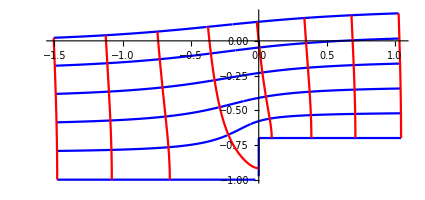

```mathematica
d=.3; h=1;
lim={-2,2,0,1.5}h;
Show[ParametricPlot[Array[ReIm@g[ξ+ⅈ #]&,6,lim⟦{3,4}⟧],{ξ,lim⟦1⟧,lim⟦2⟧},PlotStyle->{Blue},AspectRatio->Automatic],
 ParametricPlot[Array[ReIm@g[#+ⅈ η]&,8,lim⟦{1,2}⟧],{η,lim⟦3⟧,lim⟦4⟧},PlotStyle->{Red},AspectRatio->Automatic]]
```

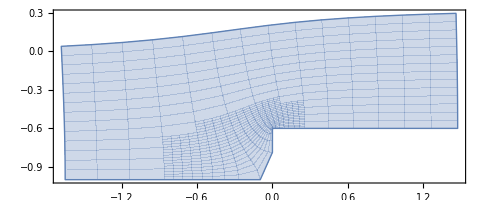

```mathematica
ParametricPlot[ReIm@g[ξ+ⅈ η],{ξ,lim⟦1⟧,lim⟦2⟧},{η,lim⟦3⟧,lim⟦4⟧}]
```